```mathematica
Clear[vLikelihood]
```

```mathematica
vPriorTriangular[θ_] := If[θ≤ 0.5,4θ,4-4θ]
vPriorFlat[θ_] := PDF[UniformDistribution[{0,0.45}],θ]
vPrior[θ_]:=If[θ≤0.45,vPriorFlat[θ],0]
```

```mathematica
vIsInteger[z_]:=If[IntegerQ[Rationalize[z]],1,0]
```

```mathematica
vLikelihood[θ_,z_]=Likelihood[BinomialDistribution[100,θ],{z}]*vPrior[θ]
```

If[θ≤0.45,vPriorFlat[θ],0] (Piecewise[{{(1-θ)^(100-z) θ^z Binomial[100,z], 0≤z≤100}, {0, True}}])

```mathematica
vLikelihood1[θ_]:=Likelihood[BinomialDistribution[100,θ],{40}]
```

```mathematica
vNumerator[θ_] := vPrior[θ]*vLikelihood1[θ]
```

```mathematica
cDenominator = NIntegrate[vNumerator[θ],{θ,0,1}];
```

```mathematica
vPosterior[θ_] := vPrior[θ]*vLikelihood1[θ]/cDenominator
```

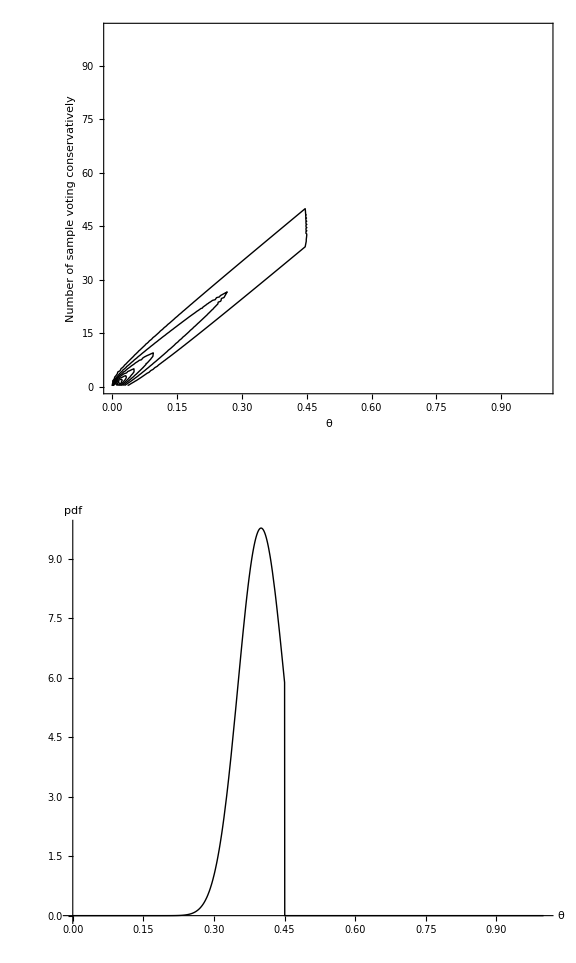

```mathematica
padding={{100,30},{30,30}};
g1=ContourPlot[vLikelihood[θ,z],{θ,0,1},{z,0,100},PlotRange->{{0,1},{0,100},{0,1}},Mesh->None,ContourShading->{White},ContourStyle->{Black},FrameLabel->{θ,"Number of sample voting conservatively"},BaseStyle->{FontSize->16},ImagePadding->padding];
g2 = Plot[vPosterior[θ],{θ,0,1},PlotRange->Full,PlotStyle->{Black},ImagePadding->padding,BaseStyle->{FontSize->16},AxesLabel->{θ,"pdf"}];
Show[GraphicsColumn[{g1,g2}],ImageSize->Large]
```